```mathematica
p[a_,b_,c_,n_]:=2*(a+b+c)^n*Exp[-(a+b+c)]/Factorial[n+2]
```

```mathematica
N[Integrate[p[a,b,10,30], {a,0,Infinity}, {b,0,Infinity}, Assumptions->{{a,b,c,n}>0,n∈Integers, {a,b,c}∈Reals}]]
```

0.0423387

```mathematica
0.475806/0.0423387
```

11.2381

```mathematica
N[Integrate[a*p[a,b,10,30], {a,0,Infinity}, {b,0,Infinity},Assumptions->{{a,b,c,n}>0,n∈Integers, {a,b,c}∈Reals}]]
```

0.475806

```mathematica
Plot3D[p[x,y,4],{x,0,10},{y,0,10},PlotPoints->78,MaxRecursion->2,Mesh->Automatic,MeshFunctions->{#3&},MaxRecursion->1]
```

-Graphics3D-

```mathematica
p1[a_,n_]:=a^n*Exp[-a]/Factorial[n]
```

```mathematica
Integrate[a*p1[a,n],{a,0,Infinity}, Assumptions->{a∈Reals, n∈Integers, a>0,n≥0}]
```

1+n

```mathematica
N[Integrate[p1[a,20],{a,0,21}, Assumptions->{a∈Reals, n∈Integers, a>0,n≥0}]]
```

0.529026

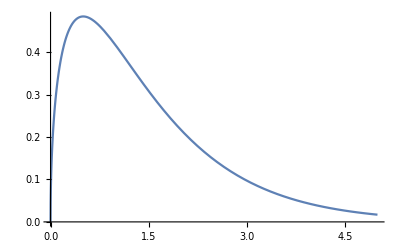

```mathematica
Plot[p1[a,0.5],{a,0,5}]
```

```mathematica
p2[a_,n_]:=a^(n-1)*Exp[-a]/Gamma[n+1]
```

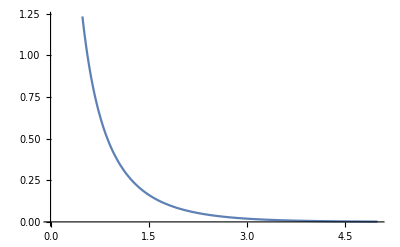

```mathematica
Plot[p2[a,0.1],{a,0,5}]
```

```mathematica
Integrate[p2[a,n], {a,n/100,n*100}]
```

(Gamma[n,n/100]-Gamma[n,100 n])/Gamma[1+n]

```mathematica
p3[rs_,rb_,n_,nb_,E1_,Et_]:= (rs*E1+rb*E1)^n*(rb*Et)^(nb-1)*Exp[-(rs*E1+rb*E1+rb*Et)]/(Gamma[n,n/100]-Gamma[n,100 n])
```

```mathematica
p5[rs_,rb_]:=p3[rs,rb,10,2000,10,1000]
```

```mathematica
p6[rs_]:=Integrate[p5[rs,rb],{rb,2000/100,2000*100}]
```

```mathematica
Plot[p6[rs],{rs,0,20}]
```

$Aborted

```mathematica
Integrate[p3[rs,rb,n,nb,E1,Et],{rb,n/c,c*n}, Assumptions->{{rs,rb,E1,Et,nb,c}>0,n≥0,n∈Integers,{rs,rb,nb,E1,Et,c}∈Reals}]
```

Integrate[(ⅇ^(-E1 rb-Et rb-E1 rs) (Et rb)^(-1+nb) (E1 rb+E1 rs)^n)/(Gamma[n,n/100]-Gamma[n,100 n]),{rb,n/c,c n},Assumptions→{{rs,rb,E1,Et,nb,c}>0,n≥0,n∈Integers,(rs|rb|nb|E1|Et|c)∈Reals}]

```mathematica
p4[rs_]:=Integrate[p3[rs,rb,n,nb,E1,Et],{rb,n/c,n*c}, Assumptions->{{rs,rb,E1,Et,nb,c}>0,n≥0,n∈Integers,{rs,rb,nb,E1,Et,c}∈Reals}]
```

```mathematica
Plot[p4[rs,10,1000,10,1000,100], {rs,0,20}]
```

$Aborted

```mathematica
Integrate[p4[rs],{rs,0,Infinity}, Assumptions->{{E1,Et,nb}>0,n≥0,n∈Integers,{rs,nb,E1,Et}∈Reals}]
```

Integrate[Integrate[ⅇ^(-E1 rb-Et rb-E1 rs) (Et rb)^(-1+nb) (E1 rb+E1 rs)^n,{rb,n/c,c n},Assumptions→{{rs,rb,E1,Et,nb,c}>0,n≥0,n∈Integers,(rs|rb|nb|E1|Et|c)∈Reals}],{rs,0,∞},Assumptions→{{E1,Et,nb}>0,n≥0,n∈Integers,(rs|nb|E1|Et)∈Reals}]

```mathematica
Gamma[-1]
```

ComplexInfinity

```mathematica
prsrb[rs_,n_,nb_,E1_,Et_,rb_]:=(rs+rb)^n*rb^(nb-1)*Exp[-rs*E1-rb*(E1+Et)]
```

```mathematica
prsrb1[rs_,rb_]:=prsrb[rs,10,1000,10,1000,rb]
```

```mathematica
N[Integrate[prsrb1[rs,rb],{rb,1,100}, Assumptions->{{rs,rb,rb0,rb1}>0,{rs,rb}∈Reals, rb0<rb1}]]
```

4.31929115054473×10^-3035 2.71828^(-10. rs) (2.0866330795×10^2594+2.03582375652501×10^2595 rs+8.94119979500491×10^2595 rs^2+2.32784434635251×10^2596 rs^3+3.97855176755343×10^2596 rs^4+4.66423341039532×10^2596 rs^5+3.79849400703532×10^2596 rs^6+2.1218841436185×10^2596 rs^7+7.78098464462436×10^2595 rs^8+1.69135418160264×10^2595 rs^9+1.65491448340793×10^2594 rs^10)

```mathematica
Integrate[prsrb[rs,n,nb,E1,Et,rb],{rb,rb0,rb1}, Assumptions->{{rs,nb,E1,Et,rb,rb0,rb1}>0, n≥0,n∈Integers, rb0<rb1, {rs,nb,E1,Et,rb,rb0,rb1}∈Reals}]
```

Integrate[ⅇ^(-(E1+Et) rb-E1 rs) rb^(-1+nb) (rb+rs)^n,{rb,rb0,rb1},Assumptions→{{rs,nb,E1,Et,rb,rb0,rb1}>0,n≥0,n∈Integers,rb0<rb1,(rs|nb|E1|Et|rb|rb0|rb1)∈Reals}]